# STATISTIKA DELNIC

## VREDNOST DELNIC

## VREDNOSTI DELNIC POSAZMEZNIH PODJETIJ SKOZI ENO LETO

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Tea\Documents\ROM\ROM2\projekt_1

#### KRKA

```mathematica
krka2018 = TableForm[Import["krka.xlsx", {"Sheets", "2018"}]];
```

```mathematica
krka2017 = TableForm[Import["krka.xlsx", {"Sheets", "2017"}]];
```

```mathematica
krka2016 =  TableForm[Import["krka.xlsx", {"Sheets", "2016"}]];
```

```mathematica
krka2015 =  TableForm[Import["krka.xlsx", {"Sheets", "2015"}]];
```

```mathematica
krka2014 = TableForm[Import["krka.xlsx", {"Sheets", "2014"}]];
```

#### MERCATOR

```mathematica
mercator2018 = TableForm[Import["mercator.xlsx", {"Sheets", "2018"}]];
```

```mathematica
mercator2017 = TableForm[Import["mercator.xlsx", {"Sheets", "2017"}]];
```

```mathematica
mercator2016 = TableForm[Import["mercator.xlsx", {"Sheets", "2016"}]];
```

```mathematica
mercator2015 = TableForm[Import["mercator.xlsx", {"Sheets", "2015"}]];
```

```mathematica
mercator2014 = TableForm[Import["mercator.xlsx", {"Sheets", "2014"}]];
```

#### LUKA KOPER

```mathematica
lukaKoper2018 = TableForm[Import["luka koper.xlsx", {"Sheets", "2018"}]];
```

```mathematica
lukaKoper2017 = TableForm[Import["luka koper.xlsx", {"Sheets", "2017"}]];
```

```mathematica
lukaKoper2016 = TableForm[Import["luka koper.xlsx", {"Sheets", "2016"}]];
```

```mathematica
lukaKoper2015 = TableForm[Import["luka koper.xlsx", {"Sheets", "2015"}]];
```

```mathematica
lukaKoper2014 = TableForm[Import["luka koper.xlsx", {"Sheets", "2014"}]];
```

#### TELEKOM SLOVENIJE

```mathematica
telekomSlo2018 = TableForm[Import["telekom slovenije.xlsx", {"Sheets", "2018"}]];
```

```mathematica
telekomSlo2017 = TableForm[Import["telekom slovenije.xlsx", {"Sheets", "2017"}]];
```

```mathematica
telekomSlo2016 = TableForm[Import["telekom slovenije.xlsx", {"Sheets", "2016"}]];
```

```mathematica
telekomSlo2015 = TableForm[Import["telekom slovenije.xlsx", {"Sheets", "2015"}]];
```

```mathematica
telekomSlo2014 = TableForm[Import["telekom slovenije.xlsx", {"Sheets", "2014"}]];
```

#### PETROL

```mathematica
petrol2018 = TableForm[Import["petrol.xlsx", {"Sheets", "2018"}]];
```

```mathematica
petrol2017 = TableForm[Import["petrol.xlsx", {"Sheets", "2017"}]];
```

```mathematica
petrol2016 = TableForm[Import["petrol.xlsx", {"Sheets", "2016"}]];
```

```mathematica
petrol2015 = TableForm[Import["petrol.xlsx", {"Sheets", "2015"}]];
```

```mathematica
petrol2014 = TableForm[Import["petrol.xlsx", {"Sheets", "2014"}]];
```

## GRAFIČNI PRIKAZ DELNIC POSAZMEZNIH PODJETIJ

#### FUNKCIJE

```mathematica
(*odstranimo vrsto z opisom podatkov*)
```

```mathematica
Naslovi[podatki_]:=podatki//First
```

```mathematica
Podatki[podatki_]:=podatki//Rest
```

```mathematica
(*Indeks stolpca*)
```

```mathematica
IndeksStolpca[podatki_,stolpec_]:=Position[Naslovi[podatki],stolpec]//First//First
```

```mathematica
(*Vrstica*)
```

```mathematica
Vrstica[podatki_,i_]:=Podatki[podatki][[i]]
```

```mathematica
(*Stolpec*)
```

```mathematica
Stolpec[podatki_, stolpec_]:= Transpose[Podatki[podatki]][[IndeksStolpca[podatki,stolpec]]]
```

```mathematica
(*Dodaj stolpec*)
```

```mathematica
DodajStolpec[podatki_,ime_,podStolpec_]:= Append[Transpose[podatki], Prepend[podStolpec, ime]] // Transpose
```

#### KRKA

```mathematica
(*krka2018G - G označuje podatke ki bodo prikazani grafično *)
```

```mathematica
krka2018G = Import["krka.xlsx", {"Sheets", "2018"}];
```

```mathematica
Naslovi[krka2018G]
```

{Datum,Odpiralni tečaj,Najvišji tečaj,Najnižji tečaj,Uradni tečaj,Promet v €,Slovenski blue chip indeks v točkah}

```mathematica
Podatki[krka2018G];
```

```mathematica
IndeksStolpca[krka2018G, "Uradni tečaj"]
```

5

```mathematica
Vrstica[krka2018G, 5]
```

{Mon 8 Jan 2018 00:00:00GMT+1.,56.,57.,56.,56.8,208802.,807.89}

PRIKAZ GIBANJA DELNICE KRKA LETA 2018

```mathematica
krka2018grafP = Transpose[{Stolpec[krka2018G, "Datum"],Stolpec[krka2018G, "Uradni tečaj"]}];
```

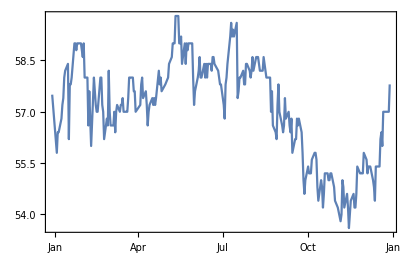

```mathematica
DateListPlot[krka2018grafP]
```

PRIKAZ GIBANJA SLOVENSKEGA BLUE CHIP INDKESA LETA 2018

```mathematica
blueChip2018 = Transpose[{Stolpec[krka2018G, "Datum"], Stolpec[krka2018G, "Slovenski blue chip indeks v točkah"]}];
```

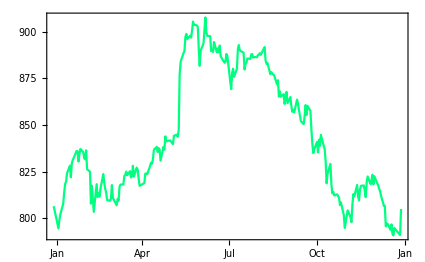

```mathematica
DateListPlot[blueChip2018 , PlotStyle->RGBColor[0,1,0.5]]
```

RAZLAGA GIBANJA

Ko primerjamo graf delince podjetja in graf blue chip indeksa, je pomembno, da se giba premo sorazmerno. Tako lahko obrazložimo, če na primer graf delnice pada in graf blue chipa pada je to smiselno. Zanimivi deli so tisti kjer se dogaja ravno obratno. Na primer, da graf delnice raste, graf blue chipa pa pada. Tu se vprašamo, zakaj točno graf delnice raste. Ali je podjetje nekako prepričalo svoje delničarje da investirajo, čeprav vrednost borze pada. Konkretno si ta primer lahko ogledamo prav na teh dveh grafih, in sicer na koncu leta 2018, je vrednsot delnice Krka malo padla a zelo hitro zrasla, borza pa padla dosti več in rasla zelo počasneje. Tu bi morda lahko tudi reki da je Krka ‘povlekla’ blue chip navzgor z svojim uspehom. Na našem trgu je to mogoče, saj imamo le 9 velikih podjetij ki so v prvi kotaciji, in spremembe vsakega od njih lahko vplivajo na stanje borze. A če pogledamo na Ameriško borzo je to praktično nemogoče, saj je zelo več delniških družb, in padec ali rast ene, ne naredi skoraj nobene spremembe.

PRIKAZ GIBANJA DELNICE KRKA 2014 - 2018

```mathematica
krka2017G = Import["krka.xlsx", {"Sheets", "2017"}];
```

```mathematica
krka2016G = Import["krka.xlsx", {"Sheets", "2016"}];
```

```mathematica
krka2015G = Import["krka.xlsx", {"Sheets", "2015"}];
```

```mathematica
krka2014G = Import["krka.xlsx", {"Sheets", "2014"}];
```

```mathematica
krka18 = Stolpec[krka2018G, "Uradni tečaj"];
```

```mathematica
krka17 = Stolpec[krka2017G, "Uradni tečaj"];
```

```mathematica
krka16 = Stolpec[krka2016G, "Uradni tečaj"];
```

```mathematica
krka15 = Stolpec[krka2015G, "Uradni tečaj"];
```

```mathematica
krka14 = Stolpec[krka2014G, "Uradni tečaj"];
```

```mathematica
DateListPlot[{krka18, krka17, krka16, krka15, krka14},{2014, 1, 1},Joined->True, PlotLabels->{"2018", "2017", "2016", "2015", "2014"}]
```

-Graphics-

```mathematica
(*x os nima pravilnih oznak*)
```

## STATISTIKA

## POVPREČNE VREDNOSTI

Povprečne vredsnoti obravnavam glede na podatke uradnega tečaja.

```mathematica
PovprecjeVrednosti[podatki_]:=Mean[Rest[Stolpec[podatki, "Uradni tečaj"]]]
```

#### KRKA

```mathematica
krka18povp = PovprecjeVrednosti[krka2018G]
```

57.0735

```mathematica
krka17povp = PovprecjeVrednosti[krka2017G]
```

54.1332

```mathematica
krka16povp = PovprecjeVrednosti[krka2016G]
```

58.8745

```mathematica
krka15povp = PovprecjeVrednosti[krka2015G]
```

62.9738

```mathematica
krka14povp = PovprecjeVrednosti[krka2014G]
```

62.7236

NAJVIŠJA POVRPEČNA VREDNOST

```mathematica
krkaMax5 = MaximalBy [Transpose[{{"Krka 2018", "Krka 2017", "Krka 2016", "Krka 2015", "Krka 2014"},{krka18povp, krka17povp, krka16povp, krka15povp, krka14povp}}], Last]
```

{{Krka 2015,62.9738}}

GRAFIČNI PRIKAZ PORAZDELITVE VREDNOSTI

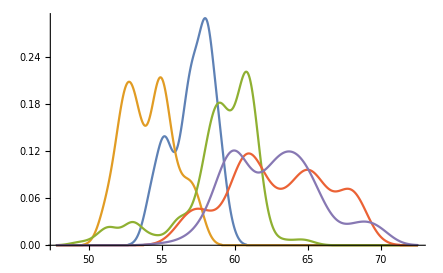

```mathematica
SmoothHistogram[{krka18, krka17, krka16, krka15, krka14}]
```

## MINIMUMI IN MAKSIMUMI

Maksimum gledamo glede na najvišji tečaj delnice. Minimum pa na najnižji tečaj.

#### KRKA

LETNI  MAX

```mathematica
krka18max = Max[Stolpec[krka2018G, "Najvišji tečaj"]]
```

60.

```mathematica
krka17max = Max[Stolpec[krka2017G, "Najvišji tečaj"]]
```

58.6

```mathematica
krka16max = Max[Stolpec[krka2016G, "Najvišji tečaj"]]
```

65.2

```mathematica
krka15max = Max[Stolpec[krka2015G, "Najvišji tečaj"]]
```

69.1

```mathematica
krka14max = Max[Stolpec[krka2014G, "Najvišji tečaj"]]
```

71.

MAX OD VSEH 5 LET

```mathematica
krkaMax5 = MaximalBy [Transpose[{{"Krka 2018", "Krka 2017", "Krka 2016", "Krka 2015", "Krka 2014"},{krka18max, krka17max, krka16max, krka15max, krka14max}}], Last]
```

{{Krka 2014,71.}}

LETNI MIN

```mathematica
krka18min = Min[Stolpec[krka2018G, "Najnižji tečaj"]]
```

53.6

```mathematica
krka17min = Min[Stolpec[krka2017G, "Najnižji tečaj"]]
```

50.09

```mathematica
krka16min = Min[Stolpec[krka2016G, "Najnižji tečaj"]]
```

48.01

```mathematica
krka15min = Min[Stolpec[krka2015G, "Najnižji tečaj"]]
```

55.8

```mathematica
krka14min = Min[Stolpec[krka2014G, "Najnižji tečaj"]]
```

51.5

MIN OD VSEH 5 LET

```mathematica
krkaMin5 = MinimalBy[Transpose[{{"Krka 2018", "Krka 2017", "Krka 2016", "Krka 2015", "Krka 2014"},{krka18min, krka17min, krka16min, krka15min, krka14min}}], Last]
```

{{Krka 2016,48.01}}

## STATISTIKA ZA VLAGATELJA

Izrazi so v angleščini, ker dosti izazov v slovenskem prevodu ni ali pa se jih ne uporablja.

PRICE TO EARNINGS RATIO

P/E razmerje pomaga investitorjem določiti vrednost delnice na trgu v primerjavi z dobičkom podjetja. Pove nam koliko je trg pripravljen plačati za delnico, na podlagi preteklega in prihodnjega finančnega stanja podjetja.  
Visok P/E lahko pomeni da je cena delnice previsoka v primerjavi z dobičkom podjetja in posledično precenjena. 
Nizek P/E lahko pomeni da je tretnutna cena delnice prenizka v primerjavi z dobičkom podjetja.

```mathematica
priceTOearnigns[povp_, dividendaSez_, i_] :=  povp / Podatki[dividendaSez][[1]][[i]]
```

PRICE TO BOOK RATIO

P/B razmerje meri ali je delnica precenejena ali podcenjena na podlagi primerjave čistih sredstev podjetja z ceno vseh delnic. 
P/B razmerje je dober pokazatelj koliko so investitorji pripravljeni plačati za vsak dolar čistih stredstev podjetja. 
Razmerje razdeli ceno delnice na čista sredstva podejtaj , ali bilančno vsoto minus obveznosti podjetja. 

Razlog, zakaj je to razmerje tako pomembno je ker pokaže razliko med vrednstjo delnice na trgu in njene knjigovodske vrednosti. Tržna vrednost je cena ki so jo investitorji pripravljeni plačati na podlagi prihodnjih zaslužkov podjetja. Vendar, pa je knjigovodska vrednost izpeljana iz sredstev podjetja in je bolj konzervativno merilo vrednosti podjetja.

```mathematica
priceTObook[povp_, knjigovodskaSez_, i_] :=  povp / Podatki[knjigovodskaSez][[1]][[i]]
```

DEBT TO EQUITY

Razmerje med dolgom in lastniškim kapitalom podjetja pomaga investitorjem določiti kako podjetje financira svoja čista sredstva. Razmerje prikazuje delež kapitala v dolgu, ki ga podjetje uporablja za financiranje svojih sredstev.  
Nizek D/E razmerje kaže, da podjetje uprorablja manjši delež dolžniškega kapitala za financiranje v pirmerjavi z lastniškim kapitalom prek delničarjev. 
Visoko razmerje med dolžniškim in lastniškim kapitalom pomeni, da podjetje več financira iz dolga glede na lastniški kapital. Preveč dolga lahko predstavlja tveganje za družbo, če nimajo zaslužka ali denarnega toka za izpolnitev svojih dolžniških obveznosti.

```mathematica
debtTOequity[podatki_, i_]:=First[({podatki[[i]][[2]]}/{podatki[[i]][[3]]})//N]
```

FREE CASH FLOW

Prosti denarni tok je denar, ki ga podjetje ustvari s svojim poslovanjem, zmanjšano za stroške izdatkov. Z drugimi besedami, prosti denarni tok ali FCF je gotovina, ki ostane po tem, ko podjetje plača svoje operativne stroške in kapitalske izdatke ali CAPEX.

Prosti denarni tok kaže, kako učinkovito podjetje ustvarja denar in je pomembno merilo pri ugotavljanju, ali ima podjetje po financiranju in kapitalskih izdatkih dovolj gotovine, da nagradi delničarje z dividendami in odkupi delnic.

PEG RATIO (PRICE TO EARNINGS TO GROWTH RATIO)

PEG je spremenjena različica razmerja P/E, ki upošteva tudi rast prihodkov. Razmerje P/E vam ne pove vedno, ali je razmerje primerno za napovedano stopnjo rasti podjetja.
Razmerje meri razmerje med ceno in dobičikom in rastjo plač. To zagotavlja celovitejšo sliko o tem, ali je cena delnice precenjena ali podcenjena z analizo današnjih prihodkov in pričakovane stopnje rasti.
Zaloga s PEG manj kot 1 je podcenjena, ker je cena nizka v primerjavi s pričakovano rastjo dobička podjetja. PEG, ki je večji od 1, se lahko šteje za precenjenega, saj lahko kaže, da je cena delnice previsoka v primerjavi s pričakovano rastjo dobička podjetja.

PRICE TO SALES RATIO

Razmerje me ceno in prodajano vrednsotjo prikazuje vrednost dolarja na borzi, ki se nanaša na vrednost prihodkov družbe. Razmerje pomeni tržna kapitalizacija ki jo dobimo tako da množimo povprečno vrednost delnice z številom delnic in to delimo z letnimi prihodki od prodaje. 
Nizko število kaže, da je cena delnice lahko podcenjena v primerjavi z njeno konkurenco, in nasprotno, veliko število kaže, da je precenjena v primerjavi s svojimi konkurenti.

Slabost tega razmerja je da ne vključuje stroškov, podjetje ima lahko boljši dobiček in slabši price to sales ratio.

## KRKA

#### PRICE TO EARNINGS RATIO

```mathematica
brutoDividendaNaDelnicoKrka = {{2017, 2016, 2015, 2014},{2.75, 2.65, 2.50, 2.10}};
```

```mathematica
brutoDividendaNaDelnicoKrka//TableForm
```

2017 | 2016 | 2015 | 2014
2.75 | 2.65 | 2.5 | 2.1

Računala bom povprečni P/E.

```mathematica
PEkrka17 = priceTOearnigns[krka17povp, brutoDividendaNaDelnicoKrka, 1]
```

19.6848

```mathematica
PEkrka16 = priceTOearnigns[krka16povp, brutoDividendaNaDelnicoKrka, 2]
```

22.2168

```mathematica
PEkrka15 = priceTOearnigns[krka15povp, brutoDividendaNaDelnicoKrka, 3]
```

25.1895

```mathematica
PEkrka14 = priceTOearnigns[krka14povp, brutoDividendaNaDelnicoKrka, 4]
```

29.8684

Najboljši P/E je bil leta 2017. Najslabši pa leta 2014.

#### PRICE TO BOOK RATIO

Računala bom povprečni P/B.

```mathematica
knjigovodskaVrednostKrka ={{2017, 2016, 2015, 2014},{45.37, 44.05, 42.87, 41.22}};
```

```mathematica
knjigovodskaVrednostKrka //TableForm
```

2017 | 2016 | 2015 | 2014
45.37 | 44.05 | 42.87 | 41.22

```mathematica
PBKrka17 = priceTObook[krka17povp, knjigovodskaVrednostKrka, 1]
```

1.19315

```mathematica
PBKrka16 = priceTObook[krka16povp, knjigovodskaVrednostKrka, 2]
```

1.33654

```mathematica
PBKrka15 = priceTObook[krka15povp, knjigovodskaVrednostKrka, 3]
```

1.46895

```mathematica
PBKrka14 = priceTObook[krka14povp, knjigovodskaVrednostKrka, 4]
```

1.52168

```mathematica
PBKrka = {PBKrka17,PBKrka16,  PBKrka15, PBKrka14}
```

{1.19315,1.33654,1.46895,1.52168}

#### DEBT TO EQUITY RATIO

```mathematica
(*Podatke jemljem za skupino Krka)
```

```mathematica
kapitalInObveznostiKrka = {{"Leto", "Lastniški kapital", "Dolžniški kapital"},{2017,1487699,431432 },{2016, 1444444, 467074},{2015, 1405984,403220} , {2014, 1351899, 443846}};
```

```mathematica
kapitalInObveznostiKrka//TableForm
```

Leto | Lastniški kapital | Dolžniški kapital
2017 | 1487699 | 431432
2016 | 1444444 | 467074
2015 | 1405984 | 403220
2014 | 1351899 | 443846

```mathematica
DEKrka17 = debtTOequity[kapitalInObveznostiKrka,2]
```

3.44828

```mathematica
DEKrka16 = debtTOequity[kapitalInObveznostiKrka,3]
```

3.09254

```mathematica
DEKrka15 = debtTOequity[kapitalInObveznostiKrka,4]
```

3.48689

```mathematica
DEKrka14 = debtTOequity[kapitalInObveznostiKrka,2]
```

3.44828

```mathematica
DEKrka = {DEKrka17, DEKrka16, DEKrka15, DEKrka14}
```

{3.44828,3.09254,3.48689,3.44828}

```mathematica
DodajStolpec[kapitalInObveznostiKrka, "D/E", DEKrka]//TableForm
```

Leto | Lastniški kapital | Dolžniški kapital | D/E
2017 | 1487699 | 431432 | 3.44828
2016 | 1444444 | 467074 | 3.09254
2015 | 1405984 | 403220 | 3.48689
2014 | 1351899 | 443846 | 3.44828

#### PRICE TO SALES RATIO

```mathematica
prodajaKrka = {{"Leto", "Prihodki od prodaje"}, {2017, 1266392}, {2016, 1174424}, {2015, 1164607}, {2014, 1191614}};
```

```mathematica
prodajaKrka//TableForm
```

Leto | Prihodki od prodaje
2017 | 1266392
2016 | 1174424
2015 | 1164607
2014 | 1191614

```mathematica
štDelnic = 32793448;
```

```mathematica
PSKrka = First[Function[prihodki, prihodki/štDelnic]/@{Stolpec[prodajaKrka, "Prihodki od prodaje"]}//N]
```

{0.0386172,0.0358128,0.0355134,0.036337}

```mathematica
DodajStolpec[prodajaKrka, "P/S", PSKrka]//TableForm
```

Leto | Prihodki od prodaje | P/S
2017 | 1266392 | 0.0386172
2016 | 1174424 | 0.0358128
2015 | 1164607 | 0.0355134
2014 | 1191614 | 0.036337

## VIRI

ČLANKI

```mathematica
Hyperlink["https://www.alphagamma.eu/finance/3-ways-use-statistics-invest-stocks/"]
```

https://www.alphagamma.eu/finance/3-ways-use-statistics-invest-stocks/

```mathematica
Hyperlink["https://www.investopedia.com/articles/fundamental-analysis/09/five-must-have-metrics-value-investors.asp"]
```

https://www.investopedia.com/articles/fundamental-analysis/09/five-must-have-metrics-value-investors.asp

PODATKI ZA STATISTIKO

```mathematica
Hyperlink["http://www.ljse.si/cgi-bin/jve.cgi?SecurityID=KRKG&doc=818"]
```

http://www.ljse.si/cgi-bin/jve.cgi?SecurityID=KRKG&doc=818

```mathematica
Hyperlink["https://www.ajpes.si/"]
```

https://www.ajpes.si/

VSEBINSKI VIRI

```mathematica
Hyperlink["https://www.investopedia.com/terms/s/stockmarket.asp"]
```

https://www.investopedia.com/terms/s/stockmarket.asp